```mathematica
DynamicModule[{f,μ,m,x,y,rts,linPar},
f=μ x - x^3;
rts=Quiet[Solve[f==0,x]]//Flatten;
Manipulate[
Show[Plot[{rts[[2]][[2]],rts[[3]][[2]]},{μ,-1,1},PlotRange->{{0,2},{-1,1}},PlotStyle->{{Black,Thick},{Black,Thick}},BaseStyle->{FontSize->12,FontFamily->"Times",Bold}],
StreamPlot[{linPar x - x^3,-y},{x,-2,2},{y,-1,1},StreamScale->0.15,PerformanceGoal->"Quality"]],{linPar,-1,1,0.01}]]
```

```mathematica
DynamicModule[{f,g,μ,m,x,y,rtsf,rtsg,linPar},
g=μ x - x^3;
f=-μ x - x^3;
rtsg=Quiet[Solve[g==0,x]]//Flatten;
rtsf=Quiet[Solve[f==0,x]]//Flatten;
Manipulate[
Show[Plot[{rtsf[[2]][[2]],rtsf[[3]][[2]]},{μ,-1,0},PlotRange->{{-2,2},{-1,1}},PlotStyle->{{Black,Thick},{Black,Thick}},BaseStyle->{FontSize->12,FontFamily->"Times",Bold}],
StreamPlot[{-linPar x - x^3,-y},{x,-2,2},{y,-1,1},StreamScale->0.15,PerformanceGoal->"Quality"]],{linPar,-1,1,0.01}]]
```

{x→0,x→-ⅈ √μ,x→ⅈ √μ}

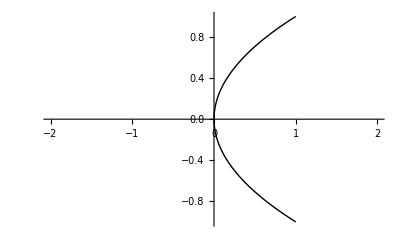

```mathematica
rtsf=Quiet[Solve[-μ x - x^3==0,x]]//Flatten
rtsg=Quiet[Solve[μ x - x^3==0,x]]//Flatten;

Plot[{rtsf[[2]][[2]],rtsf[[3]][[2]]},{μ,-1,1},PlotRange->{{-2,2},{-1,1}},PlotStyle->{{Black,Thick},{Black,Thick}},BaseStyle->{FontSize->12,FontFamily->"Times",Bold}]

Plot[{rtsg[[2]][[2]],rtsg[[3]][[2]]},{μ,-1,1},PlotRange->{{-2,2},{-1,1}},PlotStyle->{{Black,Thick},{Black,Thick}},BaseStyle->{FontSize->12,FontFamily->"Times",Bold}]
```